```mathematica
$Assumptions=Element[z,Reals] && z>0 && z<1
```

z∈ℝ&&z>0&&z<1

```mathematica
<<HPL`
```

*-*-*-*-*-* HPL 2.0 *-*-*-*-*-*

Author: Daniel Maitre, University of Zurich

Rules for minimal set loaded for weights: 2, 3, 4, 5, 6.

Rules for minimal set for + - weights loaded for weights: 2, 3, 4, 5, 6.

Table of MZVs loaded up to weight 6

Table of values at I loaded up to weight 6

$HPLFunctions gives a list of the functions of the package.
$HPLOptions gives a list of the options of the package.

More info in hep-ph/0507152, hep-ph/0703052 and at 
 http://krone.physik.unizh.ch/~maitreda/HPL/

```mathematica
ClearAll[RefineCode]
RefineCode=RawBoxes[Replace[ToBoxes@#,InterpretationBox[a_,b_,c___]:>With[{aa=StringReplace[a,{"Sqrt"->"sqrt","Power(E,"->"exp(","Power"->"pow", "nf"->"_nf","PolyLog(2,"->"dilog(","PolyLog(3,"->"wgplg(2,1,","Log"->"log","zeta[2]"->"zeta2","zeta(2)"->"zeta2","zeta[3]"->"zeta3","Zeta(3)"->"zeta3","zeta(3)"->"zeta3","zeta[4]"->"zeta4","zeta(4)"->"zeta4","Pi"->"M_PI"}]},aa],{0,Infinity}]]&;
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/vbertone/Codes/apfelxx/doc/src/codes

Import matching functions

```mathematica
Import["TMDpdf.m"];
```

Define “pure” matching function by removing all logs of the scales

```mathematica
Cqq[z_]=Series[TMDpdfqq[z]/.Lp->0/.Lh->0/.Nf->nf/.TF->TR,{as,0,3}];
```

```mathematica
Cqg[z_]=2Series[TMDpdfqg[z]/.Lp->0/.Lh->0/.Nf->nf/.TF->TR,{as,0,3}];
```

```mathematica
Cqqb[z_]=Series[TMDpdfqqb[z]/.Lp->0/.Lh->0/.Nf->nf/.TF->TR,{as,0,3}];
```

```mathematica
Cqqp[z_]=Series[TMDpdfqqp[z]/.Lp->0/.Lh->0/.Nf->nf/.TF->TR,{as,0,3}];
```

```mathematica
Cqqbp[z_]=Series[TMDpdfqqbp[z]/.Lp->0/.Lh->0/.Nf->nf/.TF->TR,{as,0,3}];
```

# O(1)

```mathematica
Cqq0[z_]=SeriesCoefficient[Cqq[z],0]
```

delta[1-z]

```mathematica
Cqg0[z_]=SeriesCoefficient[Cqg[z],0]
```

0

```mathematica
Cqqb0[z_]=SeriesCoefficient[Cqqb[z],0]
```

0

```mathematica
Cqqp0[z_]=SeriesCoefficient[Cqqp[z],0]
```

0

```mathematica
Cqqbp0[z_]=SeriesCoefficient[Cqqbp[z],0]
```

0

# O(alpha_s)

```mathematica
Cqq1[z_]=SeriesCoefficient[Cqq[z],1]
```

-2 CF (-1+z)-CF delta[1-z] zeta[2]

```mathematica
Cqg1[z_]=SeriesCoefficient[Cqg[z],1]
```

-8 TR (-1+z) z

```mathematica
Cqqb1[z_]=SeriesCoefficient[Cqqb[z],1]
```

0

```mathematica
Cqqp1[z_]=SeriesCoefficient[Cqqp[z],1]
```

0

```mathematica
Cqqbp1[z_]=SeriesCoefficient[Cqqbp[z],1]
```

0

# O(alpha_s^2)

Original expressions

```mathematica
Oqg2[z_]=SeriesCoefficient[Cqg[z],2];
```

```mathematica
Oqq2[z_]=SeriesCoefficient[Cqq[z],2];
```

```mathematica
Oqqb2[z_]=SeriesCoefficient[Cqqb[z],2];
```

```mathematica
Oqqp2[z_]=SeriesCoefficient[Cqqp[z],2];
```

```mathematica
Oqqbp2[z_]=SeriesCoefficient[Cqqbp[z],2];
```

Expressions in terms of simpler functions

```mathematica
Cqg2[z_]=HPLConvertToKnownFunctions[SeriesCoefficient[Cqg[z],2]];
```

```mathematica
Cqq2[z_]=HPLConvertToKnownFunctions[SeriesCoefficient[Cqq[z],2]];
```

```mathematica
Cqqb2[z_]=HPLConvertToKnownFunctions[SeriesCoefficient[Cqqb[z],2]];
```

```mathematica
Cqqp2[z_]=HPLConvertToKnownFunctions[SeriesCoefficient[Cqqp[z],2]];
```

```mathematica
Cqqbp2[z_]=HPLConvertToKnownFunctions[SeriesCoefficient[Cqqbp[z],2]];
```

Now construct Singlet and Valence coefficient functions

```mathematica
OqqbS2[z_]=Oqqbp2[z];
```

```mathematica
OqqS2[z_]=Oqqp2[z];
```

```mathematica
OqqbV2[z_]=Oqqb2[z]-Oqqbp2[z];
```

```mathematica
OqqV2[z_]=Oqq2[z]-Oqqp2[z];
```

```mathematica
CqqbS2[z_]=Cqqbp2[z];
```

```mathematica
CqqS2[z_]=Cqqp2[z];
```

```mathematica
CqqbV2[z_]=Cqqb2[z]-Cqqbp2[z];
```

```mathematica
CqqV2[z_]=Cqq2[z]-Cqqp2[z];
```

```mathematica
Collect[Simplify[Coefficient[OqqV2[z],delta[1-z]]],{CA,CF,TR}];
```

```mathematica
Collect[Simplify[Coefficient[OqqV2[z],plusD[0,1-z]]],{CA,CF,TR}];
```

```mathematica
Print[Collect[OqqV2[z]/.plusD[0,1-z]->0/.delta[1-z]->0+OqqbV2[z]+nf(OqqS2[z]+OqqbS2[z]),{CA,CF,TR}]];
```

CF nf TR (-4/27 (37+19 z)+(20 (1+z^2) HPL[{0},z])/(9 (1-z))+(4 (1+z^2) HPL[{0,0},z])/(3 (1-z)))+CF^2 (-22 (1-z)+(2 (5-13 z+16 z^2) HPL[{0},z])/(1-z)+2 z HPL[{1},z]-(2 (-3-2 z+2 z^2) HPL[{0,0},z])/(1-z)+2 (1+z) HPL[{0,0,0},z]+2 (1-z) (2 HPL[{2},z]+6 HPL[{1,0},z]+3 zeta[2])+2 nf^2 TR^2 ((2 (1-z) (172-143 z+136 z^2))/(27 z)+4/9 (21-30 z+32 z^2) HPL[{0},z]-2/3 (3+3 z+8 z^2) HPL[{0,0},z]+4 (1+z) HPL[{0,0,0},z]-(8 (1-z) (2-z+2 z^2) (HPL[{1,0},z]+zeta[2]))/(3 z)) (-328/81+(10 zeta[2])/3+(28 zeta[3])/9)+(4 (1+z^2) (2 HPL[{1,2},z]+2 HPL[{2,0},z]+HPL[{2,1},z]-HPL[{1,0,0},z]+2 HPL[{1,1,0},z]+6 zeta[3]))/(1-z))-5/2 CF^4 (-15 (1-z)+(-3-11 z) HPL[{0},z]+4 (1+z) HPL[{-1,0},z]+4 (1-z) HPL[{1,0},z]-2 (-3+z) zeta[2]-(2 (1+z^2) (4 HPL[{-2,0},z]-2 HPL[{2,0},z]-4 HPL[{-1,-1,0},z]+2 HPL[{-1,0,0},z]-HPL[{0,0,0},z]-2 HPL[{-1},z] zeta[2]+zeta[3]))/(1+z)) zeta[4]+CA^2 CF^2 (-15 (1-z)+(-3-11 z) HPL[{0},z]+4 (1+z) HPL[{-1,0},z]+4 (1-z) HPL[{1,0},z]-2 (-3+z) zeta[2]-(2 (1+z^2) (4 HPL[{-2,0},z]-2 HPL[{2,0},z]-4 HPL[{-1,-1,0},z]+2 HPL[{-1,0,0},z]-HPL[{0,0,0},z]-2 HPL[{-1},z] zeta[2]+zeta[3]))/(1+z)) (1214/81-(67 zeta[2])/6-(77 zeta[3])/9+5 zeta[4])+CF^3 TR (-2 nf (-328/81+(10 zeta[2])/3+(28 zeta[3])/9) (-15 (1-z)+(-3-11 z) HPL[{0},z]+4 (1+z) HPL[{-1,0},z]+4 (1-z) HPL[{1,0},z]-2 (-3+z) zeta[2]-(2 (1+z^2) (4 HPL[{-2,0},z]-2 HPL[{2,0},z]-4 HPL[{-1,-1,0},z]+2 HPL[{-1,0,0},z]-HPL[{0,0,0},z]-2 HPL[{-1},z] zeta[2]+zeta[3]))/(1+z))+5/2 nf ((2 (1-z) (172-143 z+136 z^2))/(27 z)+4/9 (21-30 z+32 z^2) HPL[{0},z]-2/3 (3+3 z+8 z^2) HPL[{0,0},z]+4 (1+z) HPL[{0,0,0},z]-(8 (1-z) (2-z+2 z^2) (HPL[{1,0},z]+zeta[2]))/(3 z)) zeta[4])+CA (CF ((8 (100+z))/27-(2 (29-36 z+83 z^2) HPL[{0},z])/(9 (1-z))-2 z HPL[{1},z]+((-11-12 z+z^2) HPL[{0,0},z])/(3 (1-z))-2 (1-z) (2 HPL[{1,0},z]+3 zeta[2])+(-2 (1+z^2) (2 HPL[{1,2},z]+2 HPL[{2,0},z]+HPL[{0,0,0},z]+2 HPL[{1,1,0},z])+2 (-13+z^2) zeta[3])/(1-z))+CF^2 TR (nf (-328/81+(10 zeta[2])/3+(28 zeta[3])/9) (-15 (1-z)+(-3-11 z) HPL[{0},z]+4 (1+z) HPL[{-1,0},z]+4 (1-z) HPL[{1,0},z]-2 (-3+z) zeta[2]-(2 (1+z^2) (4 HPL[{-2,0},z]-2 HPL[{2,0},z]-4 HPL[{-1,-1,0},z]+2 HPL[{-1,0,0},z]-HPL[{0,0,0},z]-2 HPL[{-1},z] zeta[2]+zeta[3]))/(1+z))+2 nf ((2 (1-z) (172-143 z+136 z^2))/(27 z)+4/9 (21-30 z+32 z^2) HPL[{0},z]-2/3 (3+3 z+8 z^2) HPL[{0,0},z]+4 (1+z) HPL[{0,0,0},z]-(8 (1-z) (2-z+2 z^2) (HPL[{1,0},z]+zeta[2]))/(3 z)) (1214/81-(67 zeta[2])/6-(77 zeta[3])/9+5 zeta[4]))+CF^3 (5/4 (-15 (1-z)+(-3-11 z) HPL[{0},z]+4 (1+z) HPL[{-1,0},z]+4 (1-z) HPL[{1,0},z]-2 (-3+z) zeta[2]-(2 (1+z^2) (4 HPL[{-2,0},z]-2 HPL[{2,0},z]-4 HPL[{-1,-1,0},z]+2 HPL[{-1,0,0},z]-HPL[{0,0,0},z]-2 HPL[{-1},z] zeta[2]+zeta[3]))/(1+z)) zeta[4]-2 (-15 (1-z)+(-3-11 z) HPL[{0},z]+4 (1+z) HPL[{-1,0},z]+4 (1-z) HPL[{1,0},z]-2 (-3+z) zeta[2]-(2 (1+z^2) (4 HPL[{-2,0},z]-2 HPL[{2,0},z]-4 HPL[{-1,-1,0},z]+2 HPL[{-1,0,0},z]-HPL[{0,0,0},z]-2 HPL[{-1},z] zeta[2]+zeta[3]))/(1+z)) (1214/81-(67 zeta[2])/6-(77 zeta[3])/9+5 zeta[4])))

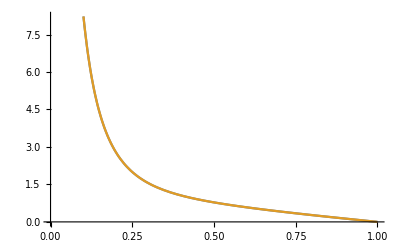

```mathematica
Plot[{OqqbS2[z]/.CF->4/3/.TR->1/2/.CA->3/.zeta[2]->Zeta[2],CqqbS2[z]/.CF->4/3/.TR->1/2/.CA->3/.zeta[2]->Zeta[2]},{z,0,1}]
```

```mathematica
Plot[{OqqS2[z]/.CF->4/3/.TR->1/2/.CA->3/.zeta[2]->Zeta[2],CqqS2[z]/.CF->4/3/.TR->1/2/.CA->3/.zeta[2]->Zeta[2]},{z,0,1}]
```

-Graphics-

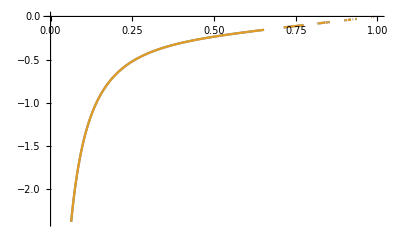

```mathematica
Plot[{OqqbV2[z]/.CF->4/3/.TR->1/2/.CA->3/.zeta[2]->Zeta[2]/.zeta[3]->Zeta[3],CqqbV2[z]/.CF->4/3/.TR->1/2/.CA->3/.zeta[2]->Zeta[2]/.zeta[3]->Zeta[3]},{z,0,1}]
```

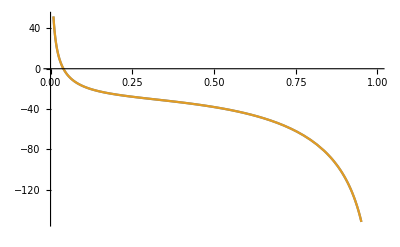

```mathematica
Plot[{OqqV2[z]/.CF->4/3/.TR->1/2/.CA->3/.zeta[2]->Zeta[2]/.zeta[3]->Zeta[3]/.zeta[4]->Zeta[4]/.nf->3/.delta[1-z]->0/.plusD[0,1-z]->0,CqqV2[z]/.CF->4/3/.TR->1/2/.CA->3/.zeta[2]->Zeta[2]/.zeta[3]->Zeta[3]/.zeta[4]->Zeta[4]/.nf->3/.delta[1-z]->0/.plusD[0,1-z]->0},{z,0,1}]
```